### 1

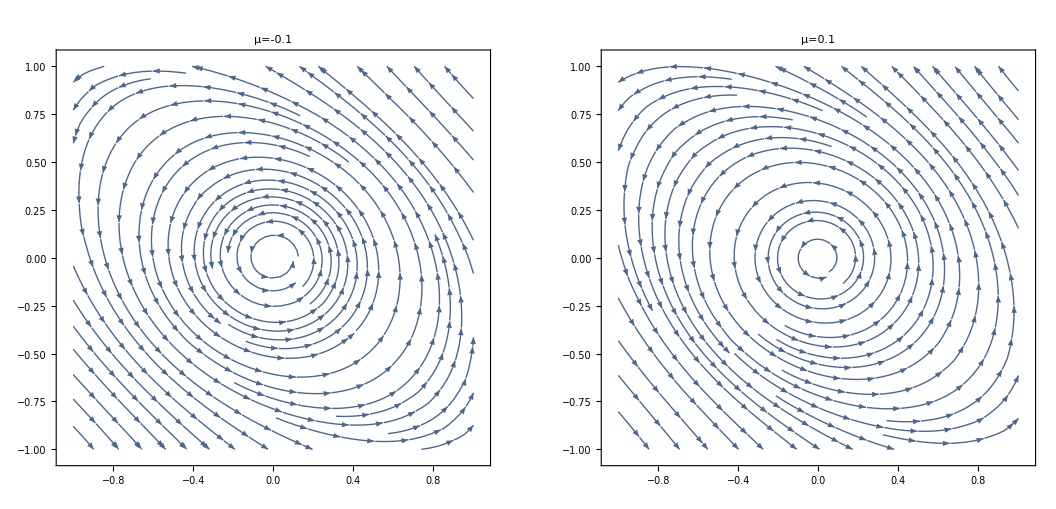

```mathematica
xDot[x_,y_,μ_] = μ x - 3y -x^3;
yDot[x_,y_,μ_] = 3x + μ y + 2y^3;
scale = 1;
tab = Table[StreamPlot[{xDot[x,y,μ],yDot[x,y,μ]},{x,-scale,scale},{y,-scale,scale}, PlotLabel->StringForm["μ=``",μ]],{μ,{-0.1,0.1}}];
GraphicsRow[tab]
```

### 2

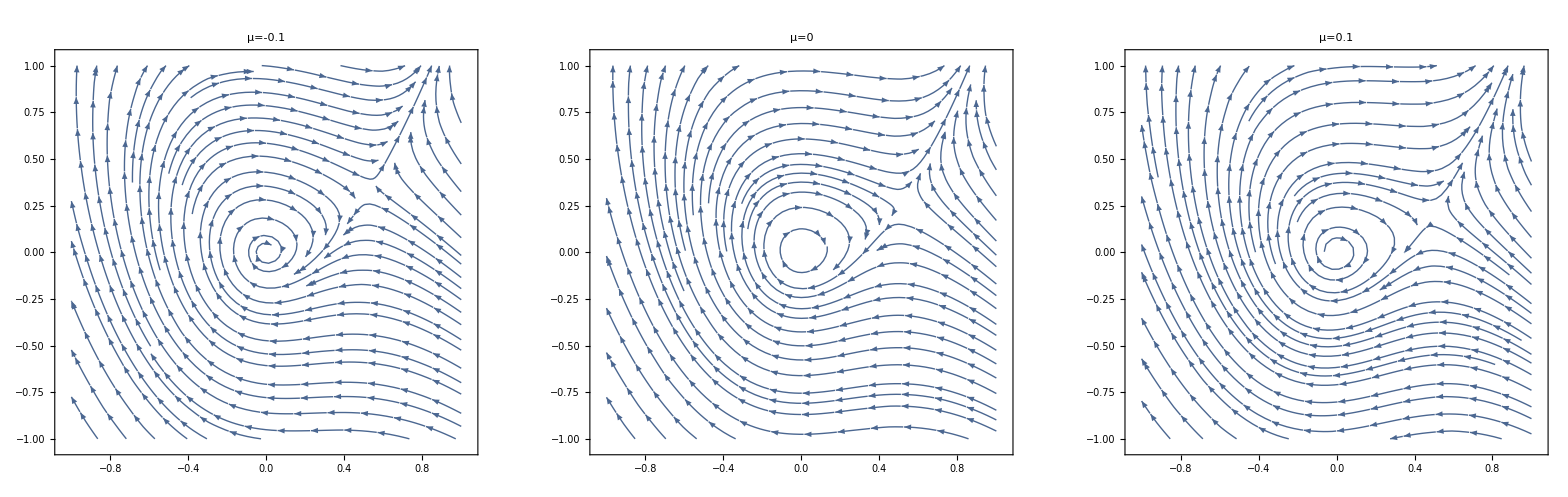

```mathematica
xDot[x_,y_,μ_] = μ x +y -x^2;
yDot[x_,y_,μ_] = -x + μ y + 2x^2;
scale = 1;
tab = Table[StreamPlot[{xDot[x,y,μ],yDot[x,y,μ]},{x,-scale,scale},{y,-scale,scale}, PlotLabel->StringForm["μ=``",μ]],{μ,{-0.1,0,0.1}}];
GraphicsRow[tab]
```